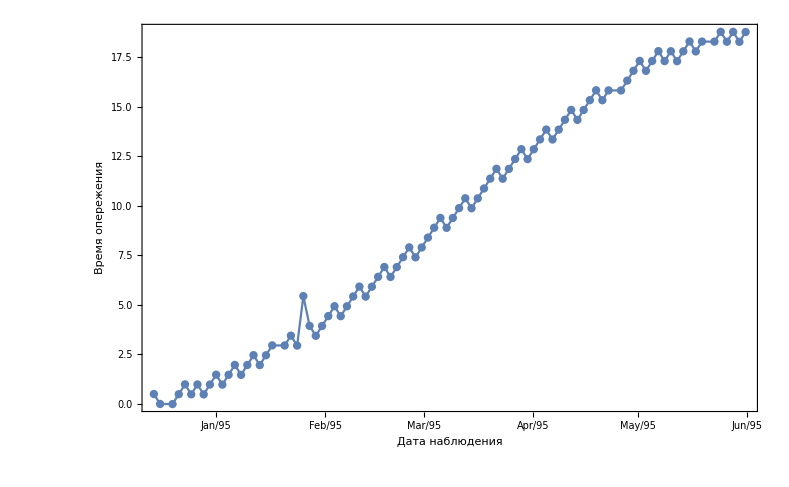

```mathematica
data=Import["~/Dropbox/Documents/Sci_pop/Roemer experiment/roemer_start.dat"];
data=data/.{}->Nothing;
data=SortBy[data,First];
data=MapAt[ToExpression@StringSplit[#,"h"]&,data,{All,3}];
data=MapAt[Reverse[ToExpression@StringSplit[#,"/"]]&,data,{All,2}];
data=DateObject[DateObject[#⟦2⟧],TimeObject[#⟦3⟧]]&/@data;//Quiet
dates=data;
SetSystemOptions["DataOptions"->"ReturnQuantities"->False];
data=Table[DateDifference[data⟦2⟧,data⟦i⟧],{i,Length[data]}];
(*ListPlot[data]*)
datanew=Table[1.76979 (i-1),{i,0,Length[data]-1}];
dataplot=Thread[{dates,24 60(datanew-data)}];
dataplot=Select[dataplot,#⟦2⟧<20&&#⟦2⟧>-1&];
(*dataplot=Drop[dataplot,{23}];*)
DateListPlot[dataplot,Mesh->Full,
DateTicksFormat->{"MonthNameShort","/","YearShort"},
LabelStyle->Medium(*,PlotRange->{Automatic,{-1,20}}*),
GridLines->Automatic,FrameLabel->{"Дата наблюдения","Время опережения"}
]
```

```mathematica
datanew
```

{-1.76979,0.,1.76979,3.53958,5.30937,7.07916,8.84895,10.6187,12.3885,14.1583,15.9281,17.6979,19.4677,21.2375,23.0073,24.7771,26.5469,28.3166,30.0864,31.8562,33.626,35.3958,37.1656,38.9354,40.7052,42.475,44.2447,46.0145,47.7843,49.5541,51.3239,53.0937,54.8635,56.6333,58.4031,60.1729,61.9427,63.7124,65.4822,67.252,69.0218,70.7916,72.5614,74.3312,76.101,77.8708,79.6406,81.4103,83.1801,84.9499,86.7197,88.4895,90.2593,92.0291,93.7989,95.5687,97.3385,99.1082,100.878,102.648,104.418,106.187,107.957,109.727,111.497,113.267,115.036,116.806,118.576,120.346,122.116,123.885,125.655,127.425,129.195,130.964,132.734,134.504,136.274,138.044,139.813,141.583,143.353,145.123,146.893,148.662,150.432,152.202,153.972,155.742,157.511,159.281,161.051,162.821,164.59,166.36}

```mathematica
data
```

{Tue 14 Dec 94 08:37GMT-5.,Thu 16 Dec 94 03:06GMT-5.,Mon 17 Dec 96 21:34GMT-5.,Sun 19 Dec 94 16:03GMT-5.,Tue 21 Dec 94 10:31GMT-5.,Thu 23 Dec 94 04:59GMT-5.,Fri 24 Dec 94 23:28GMT-5.,Sun 26 Dec 94 17:56GMT-5.,Tue 28 Dec 94 12:25GMT-5.,Thu 30 Dec 94 06:53GMT-5.,Sat 1 Jan 95 01:21GMT-5.,Sun 2 Jan 95 19:50GMT-5.,Tue 4 Jan 95 14:18GMT-5.,Thu 6 Jan 95 08:46GMT-5.,Sat 8 Jan 95 03:15GMT-5.,Sun 9 Jan 95 21:43GMT-5.,Tue 11 Jan 95 16:11GMT-5.,Thu 13 Jan 95 10:40GMT-5.,Sat 15 Jan 95 05:08GMT-5.,Sun 16 Jan 95 23:36GMT-5.,Wed 18 Jan 96 18:05GMT-5.,Thu 20 Jan 95 12:33GMT-5.,Sat 22 Jan 95 07:01GMT-5.,Mon 24 Jan 95 01:30GMT-5.,Tue 25 Jan 95 19:56GMT-5.,Thu 27 Jan 95 14:26GMT-5.,Sat 29 Jan 95 08:55GMT-5.,Mon 31 Jan 95 03:23GMT-5.,Tue 1 Feb 95 21:51GMT-5.,Thu 3 Feb 95 16:19GMT-5.,Sat 5 Feb 95 10:48GMT-5.,Mon 7 Feb 95 05:16GMT-5.,Tue 8 Feb 95 23:44GMT-5.,Thu 10 Feb 95 18:12GMT-5.,Sat 12 Feb 95 12:41GMT-5.,Mon 14 Feb 95 07:09GMT-5.,Wed 16 Feb 95 01:37GMT-5.,Thu 17 Feb 95 20:05GMT-5.,Sat 19 Feb 95 14:34GMT-5.,Mon 21 Feb 95 09:02GMT-5.,Wed 23 Feb 95 03:30GMT-5.,Thu 24 Feb 95 21:58GMT-5.,Sat 26 Feb 95 16:27GMT-5.,Mon 28 Feb 95 10:55GMT-5.,Wed 2 Mar 95 05:23GMT-5.,Thu 3 Mar 95 23:51GMT-5.,Sat 5 Mar 95 18:19GMT-5.,Mon 7 Mar 95 12:48GMT-5.,Wed 9 Mar 95 07:16GMT-5.,Fri 11 Mar 95 01:44GMT-5.,Sat 12 Mar 95 20:12GMT-5.,Mon 14 Mar 95 14:41GMT-5.,Wed 16 Mar 95 09:09GMT-5.,Fri 18 Mar 95 03:37GMT-5.,Sat 19 Mar 95 22:05GMT-5.,Mon 21 Mar 95 16:33GMT-5.,Wed 23 Mar 95 11:02GMT-5.,Fri 25 Mar 95 05:30GMT-5.,Sat 26 Mar 95 23:58GMT-5.,Mon 28 Mar 95 18:26GMT-5.,Wed 30 Mar 95 12:55GMT-5.,Fri 1 Apr 95 07:23GMT-5.,Sun 3 Apr 95 01:51GMT-5.,Mon 4 Apr 95 20:19GMT-5.,Wed 6 Apr 95 14:48GMT-5.,Fri 8 Apr 95 09:16GMT-5.,Sun 10 Apr 95 03:44GMT-5.,Mon 11 Apr 95 22:12GMT-5.,Wed 13 Apr 95 16:41GMT-5.,Fri 15 Apr 95 11:09GMT-5.,Sun 17 Apr 95 05:37GMT-5.,Tue 19 Apr 95 00:05GMT-5.,Wed 20 Apr 95 18:34GMT-5.,Fri 22 Apr 95 13:02GMT-5.,Tue 24 Apr 96 07:30GMT-5.,Tue 26 Apr 95 01:59GMT-5.,Wed 27 Apr 95 20:27GMT-5.,Fri 29 Apr 95 14:55GMT-5.,Sun 1 May 95 09:23GMT-5.,Tue 3 May 95 03:52GMT-5.,Wed 4 May 95 22:20GMT-5.,Fri 6 May 95 16:48GMT-5.,Sun 8 May 95 11:17GMT-5.,Tue 10 May 95 05:45GMT-5.,Thu 12 May 95 00:14GMT-5.,Fri 13 May 95 18:42GMT-5.,Sun 15 May 95 13:10GMT-5.,Tue 17 May 95 07:39GMT-5.,Thu 19 May 95 02:07GMT-5.,Thu 19 May 95 20:36GMT-5.,Sun 22 May 95 15:04GMT-5.,Tue 24 May 95 09:32GMT-5.,Thu 26 May 95 04:01GMT-5.,Fri 27 May 95 22:29GMT-5.,Sun 29 May 95 16:58GMT-5.,Tue 31 May 95 11:26GMT-5.}

```mathematica
DateObject[{95,5,31},TimeObject[{11,26},TimeZone->-5.],TimeZone->-5.]-DateObject[{94,12,16},TimeObject[{3,6},TimeZone->-5.],TimeZone->-5.]
```

```mathematica
Quantity[166.34722222222223, "Days"]
```

```mathematica
Quantity[166.36026, "Days"]-Quantity[166.34722222222223, "Days"]
```

0.0130378 days

```mathematica
UnitConvert[Quantity[0.013037777777782367,"Days"],"minutes"]
```

18.7744 min

```mathematica
Quantity[166.36026, "Days"]/Quantity[1.76979, "Days"]
```

94.

```mathematica
166.36026/1.76979
```

94.